```mathematica
<<MaTeX`
```

```mathematica
T[text_, magn_:1.2]:=MaTeX[text,"Preamble"->{"\\usepackage[T2A]{fontenc}", "\\usepackage{nicefrac}"},Magnification->magn]
```

```mathematica
μ=1;a=1;
```

```mathematica
Srz[r_,x_]:=-μ/(r+a)(2 r-1);
Srr[r_,x_]:=-√(1-Srz[r, x]^2)
Stt[r_,x_]:=0
```

```mathematica
fP[r_,x_]:=(3+2a)/(2a)x^2-Abs[x]/(2 μ^2)(μ √(1-μ^2)+ArcSin[μ])
```

```mathematica
α=0.1;ρ=1;C1=1;C2=2;
```

```mathematica
P[x_]:=(2μ)/α(1-Abs[x])+Srr[ρ,x]
```

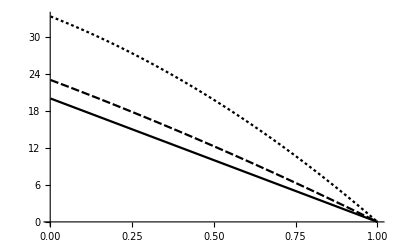

```mathematica
Plot[{P[x]-P[1],P[x]-P[1]+(C2 3)/2(1-x^2),P[x]-P[1]+(C1 3)/(α 2)(1-x^2)+fP[ρ,x]-fP[ρ,1]},{x,0.001,1},PlotTheme->"Monochrome",PlotLegends->{T["p^\\text{кв}"],T["p\\vert_{\\beta=2}"],T["p\\vert_{\\beta=1}"]},AxesLabel->{T["\\xi"],T["\\nicefrac{p}{\\tau_s}",1.5]}]//Quiet
```

```mathematica
Export["F:\\study_dissertation\\Russian-Phd-LaTeX-Dissertation-Template\\images\\ch2\\pressure_sub2.pdf",%]
```

F:\study_dissertation\Russian-Phd-LaTeX-Dissertation-Template\images\ch2\pressure_sub2.pdf